## Объявление глобальных переменных

```mathematica
SetDirectory["/Users/kirillivanov/Documents/Code/For Geant analysis/g-ne/"]
print@x_:=(Print@x;x);
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.0001;horizSize=0.0001;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

/Users/kirillivanov/Documents/Code/For Geant analysis/g-ne

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Построение одного графика

### Импорт табличных данных

```mathematica
data = Import["log.csv"];
data//TableForm
```

Energy, MeV | Sigma(E), MeV | E_gap, MeV | Sigma(E_gap), MeV
500. | 0. | 34.0218 | 0.30025
1000. | 0. | 71.5388 | 0.424584
2000. | 0. | 145.082 | 0.5855
3000. | 0. | 218.908 | 0.75043
4000. | 0. | 291.337 | 0.846708
5000. | 0. | 365.752 | 0.938121
6000. | 0. | 438.43 | 1.0356
7000. | 0. | 512.537 | 1.05923
8000. | 0. | 585.124 | 1.20964
9000. | 0. | 656.988 | 1.2374
10000. | 0. | 732.601 | 1.31174

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[-2.33237+0.073671 x-2.79439×10^-8 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -2.33237 | 0.642278 | -3.6314 | 0.00667149
x | 0.073671 | 0.000297227 | 247.861 | 7.85872×10^-17
x^2 | -2.79439×10^-8 | 2.80199×10^-8 | -0.997288 | 0.34783

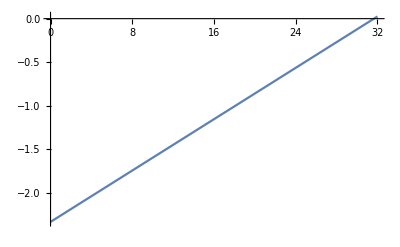

```mathematica
forFit=data⟦2;;,{1,3}⟧;
forFitCr=data⟦2;;,-1⟧;
fit2=LinearModelFit[forFit,{1,x, x^2},x]
fit2@"ParameterTable"
Plot[fit2["Function"]@x, {x, 0, 32}]
```

```mathematica
((print@fit2["FitResiduals"])/(print@forFitCr))^2
χ22=Total[(fit2["FitResiduals"]/forFitCr)^2]/(11-3)
```

{-0.474362,0.228105,0.184407,0.478987,-0.567886,0.42801,-0.257291,0.541377,-0.123747,-1.45488,1.01728}

{0.30025,0.424584,0.5855,0.75043,0.846708,0.938121,1.0356,1.05923,1.20964,1.2374,1.31174}

{2.49605,0.288631,0.0991975,0.407406,0.449836,0.208157,0.0617252,0.261226,0.0104656,1.38241,0.601435}

0.783317

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

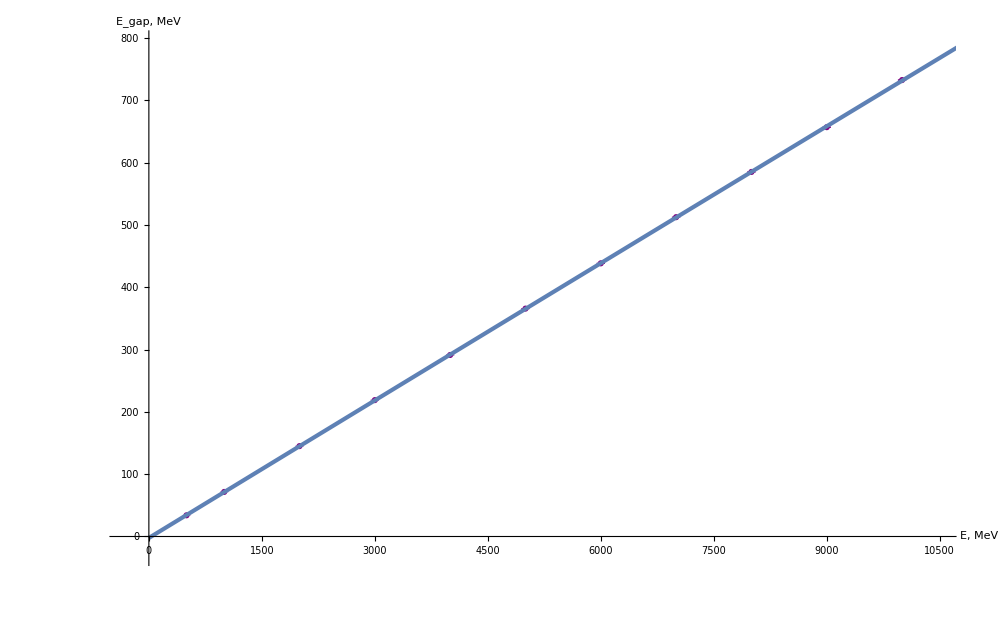

images/png/calib2.png

images/png/fit_res2.png

```mathematica
plot2 =Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.006,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{-30,795}}], 
Plot[fit2["Function"]@x,{x,0,10900}, PlotStyle->Thickness@0.003]]
Export["images/png/calib2.png",plot2,"PNG"]
Export["images/png/fit_res2.png",fit2@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportE = {fit2@"BestFitParameters",fit2@"ParameterErrors",χ22}
Export["fit_res2.csv",exportE,"CSV"]
```

{{-2.33237,0.073671,-2.79439×10^-8},{0.642278,0.000297227,2.80199×10^-8},0.783317}

fit_res2.csv

## Построение одного графика

### Импорт табличных данных

```mathematica
dataR = Import["log_red.csv"];
dataR//TableForm
```

Energy, MeV | Sigma(E), MeV | dE/E | Sigma(dE/E)
885.223 | 6.82976 | 0.1892 | 0.00376563
1359.45 | 8.31459 | 0.151853 | 0.00293576
1935.88 | 10.4174 | 0.13458 | 0.0025829
2951.7 | 12.7768 | 0.105628 | 0.00198614
3560.53 | 13.9879 | 0.0972338 | 0.00181707
4135.37 | 15.2064 | 0.0906006 | 0.00168802
5032.06 | 14.6098 | 0.0809702 | 0.00149698
6297.59 | 18.279 | 0.0746288 | 0.00137986
7179.22 | 19.167 | 0.0689296 | 0.00127198
7992.52 | 20.7233 | 0.0655305 | 0.00120895
9747.67 | 23.9489 | 0.0623377 | 0.00114838

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.00515412+5.48892/(√x)]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00515412 | 0.00158296 | 3.25599 | 0.00990201
1/(√x) | 5.48892 | 0.0833476 | 65.8557 | 2.16693×10^-13

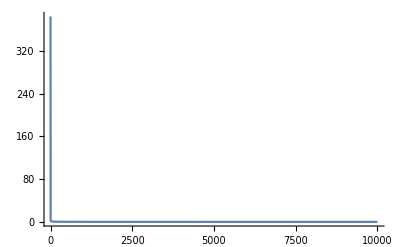

```mathematica
forFitR=dataR⟦2;;,{1,3}⟧;
fitR=LinearModelFit[forFitR,{1,1/Sqrt[x]},x]
forFitCrR=dataR⟦2;;,-1⟧;
fitR@"ParameterTable"
Plot[fitR["Function"]@x, {x, 0, 10000}, PlotRange->All]
```

```mathematica
((print@fitR["FitResiduals"])/(print@forFitCrR))^2
χR=Total[(fitR["FitResiduals"]/forFitCrR)^2]/(11-2)
```

{-0.000438799,-0.00217033,0.0046735,-0.000556597,0.0000919944,0.0000913372,-0.00156131,0.000307605,-0.00100558,-0.00102035,0.00158852}

{0.00376563,0.00293576,0.0025829,0.00198614,0.00181707,0.00168802,0.00149698,0.00137986,0.00127198,0.00120895,0.00114838}

{0.0135786,0.546523,3.27392,0.0785351,0.00256317,0.0029278,1.08779,0.0496954,0.62499,0.712324,1.91345}

0.922922

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

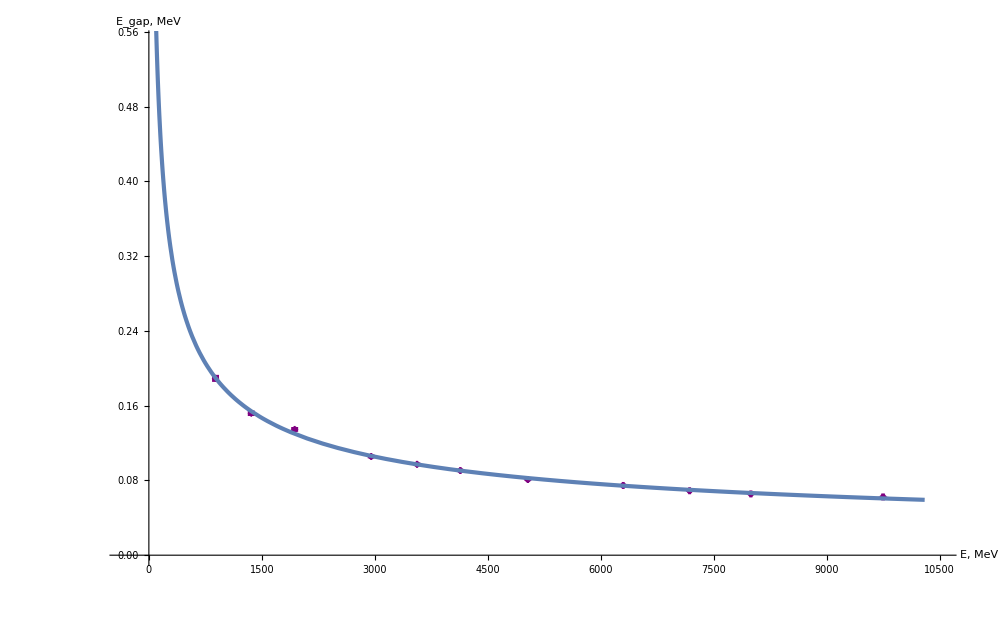

images/png/re.png

images/png/fit_re_res.png

```mathematica
plotR=Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataR⟦2;;,{1,3,2,4}⟧,
GridLines->{grids@500,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"E, MeV","E_gap, MeV"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.005,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{-300,10500},{0,0.55}}], 
Plot[fitR["Function"]@x,{x,0,10300}, PlotStyle->Thickness@0.003, PlotRange->Full]]
Export["images/png/re.png",plotR,"PNG"]
Export["images/png/fit_re_res.png",fitR@"ParameterTable","PNG"]
```

#### Экспорт фита данных в CSV формат

```mathematica
exportR = {fitR@"BestFitParameters",fitR@"ParameterErrors",χR}
Export["fit_re_res.csv",exportR,"CSV"]
```

{{0.00515412,5.48892},{0.00158296,0.0833476},0.922922}

fit_re_res.csv